Solving in the lab frame:

```mathematica
sol=First@NDSolve[{c'[t]== -I/2 c[t]-I 1/2 2π  Exp[-I  t]d[t],d'[t]== I/2 d[t]-I 1/2 2π Exp[I t]c[t],c[0]==1,d[0]==0},{c,d},{t,0,3}]
sol1=First@NDSolve[{c'[t]== -I/2 c[t]-I 1/2 2π  Exp[-I (1+2π) t]d[t],d'[t]== I/2 d[t]-I 1/2 2π Exp[I (1+2π) t]c[t],c[0]==1,d[0]==0},{c,d},{t,0,3}]
sol2=First@NDSolve[{c'[t]== -I/2 c[t]-I 1/2 2π  Exp[-I (1+2 2π) t]d[t],d'[t]== I/2 d[t]-I 1/2 2π Exp[I (1+2 2π) t]c[t],c[0]==1,d[0]==0},{c,d},{t,0,3}]
```

{c→InterpolatingFunction[…],d→InterpolatingFunction[…]}

{c→InterpolatingFunction[…],d→InterpolatingFunction[…]}

{c→InterpolatingFunction[…],d→InterpolatingFunction[…]}

Solving in the rotating frame, rotating with the drive:

```mathematica
sol=First@NDSolve[{c'[t]== -I 1/2 2π  d[t],d'[t]== -I 1/2 2π c[t],c[0]==1,d[0]==0},{c,d},{t,0,3}]
sol1=First@NDSolve[{c'[t]== -I/2(1 2π) c[t]-I 1/2 2π  d[t],d'[t]== I/2(1 2π )d[t]-I 1/2 2π c[t],c[0]==1,d[0]==0},{c,d},{t,0,3}]
sol2=First@NDSolve[{c'[t]== -I/2(2 2π) c[t]-I 1/2 2π  d[t],d'[t]== I/2(2 2π )d[t]-I 1/2 2π c[t],c[0]==1,d[0]==0},{c,d},{t,0,3}]
```

{c→InterpolatingFunction[…],d→InterpolatingFunction[…]}

{c→InterpolatingFunction[…],d→InterpolatingFunction[…]}

{c→InterpolatingFunction[…],d→InterpolatingFunction[…]}

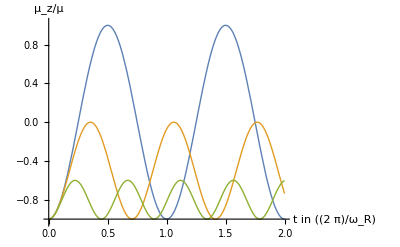

```mathematica
Plot[{-1+2 Abs[d[t]]^2/.sol,-1+2 Abs[d[t]]^2/.sol1,-1+2 Abs[d[t]]^2/.sol2},{t,0,2},PlotRange->{-1.03,1.03},PlotStyle->Thick,AxesLabel-> {t"in " [(2π)/Subscript[ω, R]],"μ_z/μ"},AxesOrigin-> {0,-1}]
```

```mathematica
Show[ParametricPlot3D[{2 Re[c[t]* d[t]],2Im[c[t]* d[t]],-1+2 Abs[d[t]]^2}/.sol,{t,0,2},PlotStyle->{Darker[Blue], Thick}], ParametricPlot3D[{2 Re[c[t]* d[t]],2Im[c[t]* d[t]],-1+2 Abs[d[t]]^2}/.sol1,{t,0,2},PlotStyle-> {Purple,Thick}], ParametricPlot3D[{2 Re[c[t]* d[t]],2Im[c[t]* d[t]],-1+2 Abs[d[t]]^2}/.sol2,{t,0,2},PlotStyle->{Darker[Yellow],Thick}],Graphics3D[{Opacity[0.2],Sphere [{0,0,0},1]}],AxesLabel->{"μ_x","μ_y","μ_z"},ViewPoint->{-.3,3,0},ViewVertical->{0,0,1}]
```

-Graphics3D-

```mathematica
Export["/Users/martin/Dropbox (MIT)/Teaching/8.421/8.421_S22/Mathfiles/RabionBlochsphere.png",%,ImageResolution->300]
```

/Users/martin/Dropbox (MIT)/Teaching/8.421/8.421_S22/Mathfiles/RabionBlochsphere.png

{c→InterpolatingFunction[…],d→InterpolatingFunction[…]}

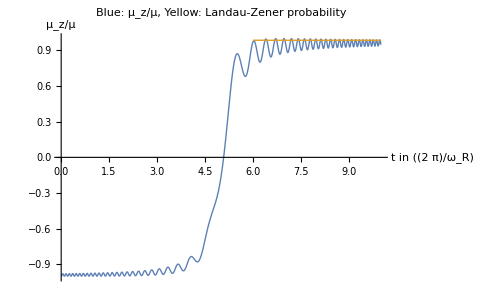

```mathematica
ω0=2π 0;
ωR = 2π 1 ;
b = .1;
ωoft[t_]:=ω0-10 ωR+20ωR b t
phioft[t_]:=Integrate[ωoft[tp],{tp,0,t}]
sol2=First@NDSolve[{c'[t]== -I/2 ω0 c[t]-I ωR/2 Exp[-I  phioft[t]]d[t],d'[t]== I/2 ω0 d[t]-I ωR/2 Exp[I phioft[t]]c[t],c[0]==1,d[0]==0},{c,d},{t,0,1/b},MaxSteps->10000]
Plot[{2 Abs[d[t]]^2-1/.sol2,
If[b t > 0.6,(1-2Exp[-π/2 ωR^2/(20ωR b)])]},{t,0,1/b},PlotRange->{-1,1},PlotStyle->Thick,AxesLabel-> {t"in " [(2π)/Subscript[ω, R]],"μ_z/μ"},PlotLabel->"Blue: μ_z/μ, Yellow: Landau-Zener probability"]
```

```mathematica
`
```

{Lx→InterpolatingFunction[…],Ly→InterpolatingFunction[…],Lz→InterpolatingFunction[…]}

ReplaceAll::reps: {sol3} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

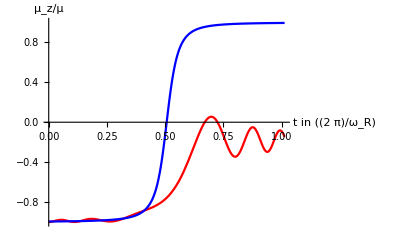

```mathematica
ω0=2π 0;
ωR = 2π 1 ;
b =.1 π^2;
ωoft[t_]:=ω0-10 ωR+20ωR b t
phioft[t_]:=Integrate[ωoft[tp],{tp,0,t}]
sol2=First@NDSolve[{Lx'[t]==Ly[t](ω0-ωoft[t]),Ly'[t]== Lz[t] ωR -Lx[t](ω0-ωoft[t]),Lz'[t]== -Ly[t]ωR,Lz[0]==-1,Ly[0]==0,Lx[0]==0},{Lx,Ly,Lz},{t,0,1/b},MaxSteps->10000]
Plot[{2 Abs[d[t]]^2-1/.sol2,Lz[t]/.sol3,
(ωoft[t]-ω0)/(√(ωR^2+(ωoft[t]-ω0)^2)),-(ωoft[t]-ω0)/(ωoft[0]-ω0),1-2Exp[-π/2 ωR^2/(20ωR b)]},{t,0,1/b},PlotRange->{-1,1},PlotStyle->Thick];
Lzplot=Plot[{Lz[t]/.sol2,
(ωoft[t]-ω0)/(√(ωR^2+(ωoft[t]-ω0)^2))},{t,0,1/b},PlotRange->{-1,1},PlotStyle->{Red,Blue},AxesLabel->{t"in " [(2π)/Subscript[ω, R]],"μ_z/μ"}]
```

```mathematica
Show[ParametricPlot3D[{Lx[t],Ly[t],Lz[t]}/.sol2,{t,1/b 0.0,1 1/b},PlotRange->{-1,1},AxesLabel->"μ_z/μ"],Graphics3D[{Opacity[0.2],Sphere [{0,0,0},1]}],AxesLabel->{"μ_x","μ_y","μ_z"},ViewPoint->{0.8,-2,1.5},ViewVertical->{0,0,1}]
```

-Graphics3D-

{c→InterpolatingFunction[…],d→InterpolatingFunction[…]}

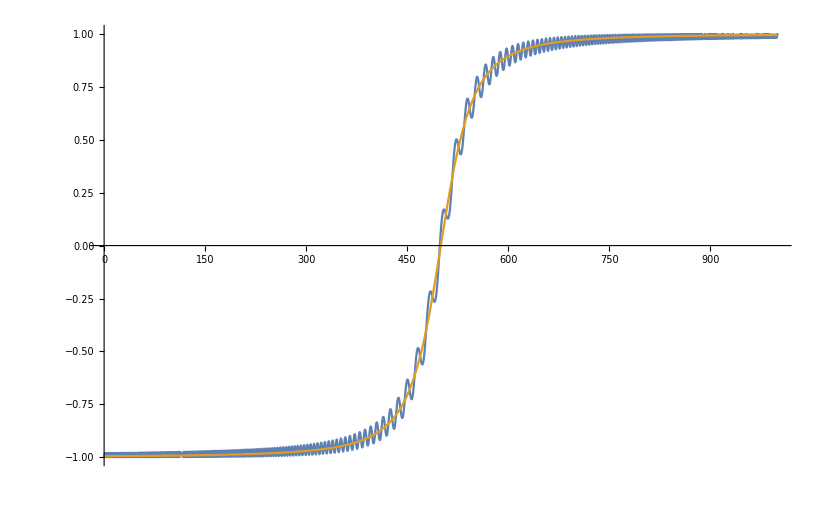

```mathematica
ω0=2π 1;
ωR = 2π 0.05 ;
b = .001;
ωoft[t_]:=ω0-10 ωR+20ωR b t
phioft[t_]:=Integrate[ωoft[tp],{tp,0,t}]
sol2=First@NDSolve[{c'[t]== -I/2 ω0 c[t]-I ωR/2 Exp[-I  phioft[t]]d[t],d'[t]== I/2 ω0 d[t]-I ωR/2 Exp[I phioft[t]]c[t],c[0]==1,d[0]==0},{c,d},{t,0,1/b},MaxSteps->50000]
Plot[{2 Abs[d[t]]^2-1/.sol2,(ωoft[t]-ω0)/(√(ωR^2+(ωoft[t]-ω0)^2))},{t,0,1/b},PlotRange->{-1,1}]
```

{c→InterpolatingFunction[…],d→InterpolatingFunction[…]}

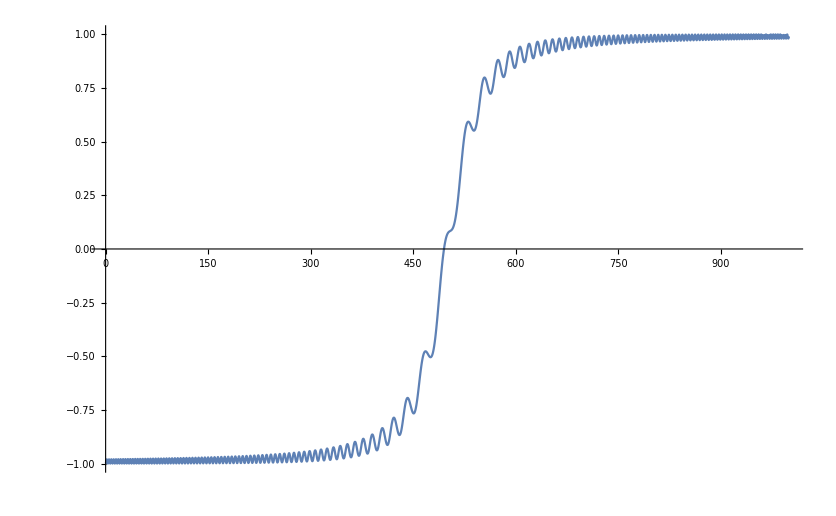

```mathematica
ω0=2π 1;
ωR = 2π 0.03 ;
b = .001;
ω0oft[t_]:=ω0-10 ωR+20ωR b t;
sol2=First@NDSolve[{c'[t]== -I/2 ω0oft[t] c[t]-I ωR/2 Exp[-I ω0 t]d[t],d'[t]== I/2 ω0oft[t] d[t]-I ωR/2 Exp[I ω0 t]c[t],c[0]==1,d[0]==0},{c,d},{t,0,1/b},MaxSteps->50000]
Plot[{2 Abs[d[t]]^2-1/.sol2},{t,0,1/b},PlotRange->{-1,1}]
```